# Stochastic globular cluster simulations of binary black hole dynamical interactions

In this notebook we present an emulator for gravitational NBODY simulations of globular clusters, given a i) black hole population N(m) and ii) initial conditions r_h, N_stars for the NBODY simulation. 
We make a comparison with state of the art globular cluster emulators by Kritos et al . https://arxiv.org/pdf/2210.10055
For reference, we will also compare with an NBODY simulation which we have at hand from DeVita et al. 2019
https://arxiv.org/pdf/1903.07619

## Constants and functions

all in SI units

### physical constants

```mathematica
Mpcm=10^6 3.0856775807 10^16;(*Mpc in meters*)
pc=3.0856775807 10^16;(*pc in m*)
c=299792458;(*speed of light,m/s*)
G=6.67428 10^-11;(*G in m^3/kg/s^2*)
Mpc=Mpcm/c;(*Gpc in seconds*)
yr=3.15569 10^7;(*year in seconds*)
AU=149597871 10^3;(*m*)
Rsun=695500000;(*m*)
Msunkg=1.98892 10^30;(*Msun in kg*)
tHubble=1.4 10^10 yr;
thubble = 14 10^9 π 10^7;
Myr = π 10^7 10^6;
```

### Cluster properties (can200k model)

```mathematica
Rh=4pc;(*Half light radius in m*)
mav=0.4;
M=2 10^5 Msunkg mav;(*total mass in kg*)
Ra=Rh/1.3;(*%Plummer sphere*)
v=(G M/Ra)^(1/2);
vesc0 = 3(G M/Rh)^(1/2);
```

Note that the black hole subcluster has a much smaller half mass radius. We take this directly from the NBODY simulation, which is not at time zero but at around 2 Gyr after the cluster has properly collapsed. 
This comes from Equation 30 in Lee https://arxiv.org/pdf/astro-ph/9409073
It is
r_(h,BH)=  0.02 8/ξmin(MBHav/10)^2 MBH/(1000 MBHav)0.64/mav 10^6/Mtot
where
ξ_min= (mbar^3 Mbar^2(27/4(1+(3 Mbar)/(2 mbar))(1+5/2 Mbar)^-3))^(1/3)
and
m_bar =(M_(BH,av))/m_av
and
M_bar =M_BH/M_tot

From the can200k simulation, there are 109 black holes,  M_(BH,av)=9.75, r_(h, BH) = 0.6 pc, m_av = 0.4, M_tot= 95,000. Then

```mathematica
NBH1=109;
Rh=4 pc;
MBHav = 9.75;
mav=0.4;
Mtot =M /Msunkg;
mbar = MBHav/mav;
Mbar = MBHav 109 /(Mtot);
ξmin=(mbar^3 Mbar^2(27/4(1+(3 Mbar)/(2 mbar))(1+5/2 Mbar)^-3))^(1/3);
rhBHLee = Rh /pc 0.04 4/ξmin(MBHav/10)^2 NBH1/1000 0.6/mav 10^6/Mtot
```

0.497066

Note that these quantities are taken from the initial conditions . But we are using them to compute a quantity once the cluster is actually collapsed (which may be Gyr later, where the quantities such as mean mass .. total cluster mass.. change slightly). So we should be careful.

### Loading the actual mass distribution of black holes in can200k

```mathematica
SetDirectory["/Users/lucym/Documents/2026/black-hole-triples"]
```

/Users/lucym/Documents/2026/black-hole-triples

```mathematica
Filename = "can200k_masses.csv";
can200kBHmass=Select[NumericQ][Import[Filename,{"Data",All,1}]];
```

### functions

Energy distribution from Stone and Leigh 2019 https://arxiv.org/abs/1909.05272

```mathematica
dista[x_]=ProbabilityDistribution[5/2 x^(3/2),{x,0,1}];
```

Eccentricities (from Stone and Leigh, around middle of page 5)

```mathematica
diste[x_]=ProbabilityDistribution[((4+π)/8)^-1 (x(1+x))/(2(1-x^2)^(1/2)),{x,0,1}];
distetherm[x_]=ProbabilityDistribution[2x,{x,0,1}];
```

We take the probability that the interloper m3 component is NOT swapped out from Ginat and Perets 2019:

```mathematica
Pswap[m11_,m22_,m33_]=(m11^4 m22^4)/((m11+m22)^(5/2)(m11^4(m33^4/(m33+m11)^(5/2)+m22^4/(m11+m22)^(5/2))+(m33^4 m22^4)/(m33+m22)^(5/2)));
```

The hardening factor if given by equation 11 in Kritos + 2024. Note equal mass case is 0.78.

## Setting up cluster population

For the mass distribution, we can roughly reproduce the can200k cluster BH population with the following

```mathematica
NBHi=140;
incluster = Table[1,{i,NBHi}];
mtemp = RandomVariate[ExponentialDistribution[0.7],NBHi]+10;
mtemp = RandomVariate[GammaDistribution[8,1.5],NBHi];
m =Pick[mtemp ,8<#<40&/@mtemp ] ;
NBH = m//Length
```

116

```mathematica
Mean[mtemp]
```

12.1767

### Pairing up black holes in binaries

Now we will pair up the black holes, given a binary fraction of 10 percent

```mathematica
fbin=0.1; 
Nbin=fbin NBH//Round
```

12

We make sure that the majority (f1 = 80%?) of BH in binaries are the most massive . But not all .

```mathematica
f1 = 0.8;
```

```mathematica
mtemp =ReverseSort[m];
```

```mathematica
min3 = mtemp[[;;Round[f1 2 Nbin]]];
```

To reorder, we delete the BH in binaries from mtemp

```mathematica
mtemp[[;;Round[f1 2 Nbin]]]=-1;
```

```mathematica
mtemp2 =Select[mtemp,#>0&];
```

mnew is our jumbled binary population, dominated by most massive

```mathematica
mnew =Join[min3,RandomSample[mtemp2[[]]]];
```

```mathematica
minbinary0 =mnew[[;;2 Nbin]];
minterlopers0  = mnew[[2 Nbin+1;;]];
```

Now pair them up randomly

```mathematica
{testArrayOdd,testArrayEven}=Partition[minbinary0,2,2,1,{}]~Flatten~{2};
```

```mathematica
Clear@groupByPositions
groupByPositions[list_,pred_]:=With[{trueList=minbinary0[[Select[Range@Length@list,pred]]]},{trueList,Complement[list,trueList]}]
{testArrayOdd,testArrayEven}=groupByPositions[minbinary0,OddQ];
```

We arrange the ones in binaries so that more massive is at an odd index.

```mathematica
diffarray = testArrayEven-testArrayOdd;
```

```mathematica
m1big = Join[Pick[testArrayEven,#>0&/@diffarray],Pick[testArrayOdd,#<0&/@diffarray] ];
```

```mathematica
m2small = Join[Pick[testArrayEven,#<0&/@diffarray],Pick[testArrayOdd,#>0&/@diffarray] ];
```

```mathematica
mbin =m1big +m2small
```

{28.0995,31.5869,33.934,37.916,38.9775,41.9123,42.0113,39.2316,38.4239,37.7216,33.2005,28.1018}

Here we plot the black hole mass distribution

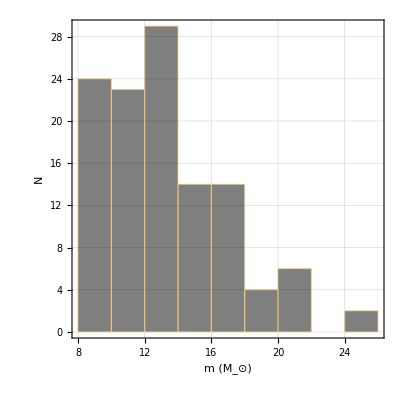

```mathematica
Histogram[mnew,ChartStyle->{Directive[Black,Opacity[.5]]},AspectRatio->1,Frame -> True,FrameLabel->{Style["m (M_⊙)",20,Black],Style["N",20,Black]},LabelStyle->{(FontFamily->"Times"),Black},GridLines->Automatic,FrameTicksStyle->Directive[FontSize->15,Black],ScalingFunctions->{None,None},BaseStyle->{FontSize->20, Black}]
```

```mathematica
mnew//Length
```

116

Print related quantities to make consistent r_(h,BH)

```mathematica
Mean[mnew]
```

13.3439

```mathematica
Mean[mnew] Length[mnew]
```

1547.89

```mathematica
NBH1 MBHav
```

1062.75

### initial binary separations and eccentricities

For the initial separations, we draw from a log Uniform distribution with a maximum of the hard - soft boundary like Morscher + 2015

```mathematica
ahard = G(m1big +m2small)Msunkg/v^2;
```

```mathematica
amin = Table[50 (Rsun+Rsun),{i,1,Length[ahard]}];
```

Initial eccentricities drawn from a thermal distribution.

```mathematica
earrbin= Sqrt[RandomReal[{0,1},Nbin]];
```

```mathematica
aarrbinlog=Table[RandomVariate[UniformDistribution[{Log[amin][[i]],Log[ahard][[i]]}]],{i,1,Length[ahard]}];
```

```mathematica
aarrbin2=Exp[aarrbinlog];
aedata =Transpose@{aarrbin2,earrbin};
```

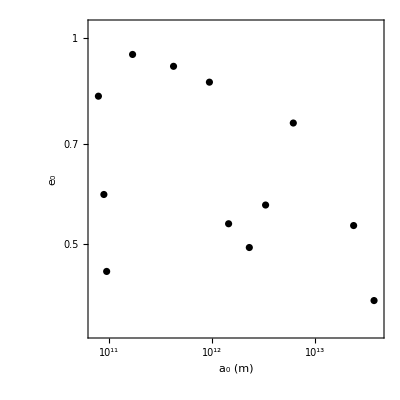

```mathematica
ListLogLogPlot[aedata,AspectRatio->1,Frame -> True,FrameLabel->{Style["a_0 (m)",20,Black],Style["e_0",20,Black]},LabelStyle->{(FontFamily->"Times"),Black},GridLines->Automatic,FrameTicksStyle->Directive[FontSize->15,Black],ScalingFunctions->{None,None},BaseStyle->{FontSize->20, Black},PlotRange->{{0.9Min[aarrbin2],1.1Max[aarrbin2]},{0.9Min[earrbin],1.1Max[earrbin]}}]
```

## Stochastic cluster simulation: super thermal eccentricity sampling, statistical hardening

We create empty lists for the number of merged binaries, and ejected binaries. We also make separate lists for the masses of merged and ejected binaries.

```mathematica
nmsto={};
nesto={};
neisto={};
m1msto={};
m2msto={};
m1esto={};
m2esto={};
aejsto={}
eejsto={}
tejsto={};
tejmergesto={};
aejmergesto={};
eejmergesto={};
timemerge = {};
nmergej={};
Nsim=1000;
```

{}

{}

Note: Flag 15 for the eccentricity: we draw from a super thermal distribution. Something optional to be confirmed(?) by rebound is any correlation between the post-interaction e and a.

Also note that currently, we don’t change the black hole sub cluster half mass radius rhBH according to ejections.

```mathematica
((*Flag 1: Initialization for a single cluster simulation*)
Niter=0;
Label[3];
merge= Table[1,{i,Nbin}];
in= Table[1,{i,Nbin}]; 
totali =0;
massinint2 ={};
massinint3 ={};
aafter = {};
totalmerge = 0;
totaleject = 0;
totalejecti=0;
totalejectmerge=0;
mbinloop =mbin ;
m1loop =m1big ;
m2loop =m2small;
aloop =aarrbin2;
eloop =earrbin;
mintloop = minterlopers0;
aej=Table[1,{i,Nbin}];
NBHi=150;
incluster = Table[1,{i,NBHi}];
rhBH0 = 0.73 pc;
rhBH =rhBH0;
rhfac = 1;
Rh=rhBH rhfac;
Ranew = Rh/1.3;
tnow=0;
nmax=thubble;

(Label[1]; 

(* Flag 2 Compute GW merger timescale for all binaries *)
tauGWloop= c^5(G^3 m1loop  m2loop(mbinloop)(Msunkg)^3)^-1(5 aloop^4)/256(1+0.27 eloop^10+0.33 eloop^20)(1-eloop^2)^(7/2);
vnew=v (Ra/Ranew)^(1/2);

NBHnow = mintloop//Length;
Ntime = 200(NBHnow/(4/3 π Rh^3));

(* Flag 3: calculate interaction time for each binary. Depends on number density (fixed)*)
tauintarrlooptmpd=vnew/(10^4/pc^3)/π/aloop/G/(mbinloop*Msunkg);
tauintarrloop=tauintarrlooptmpd ;

timeloc = With[{m=Min[tauintarrlooptmpd]},{m,Position[tauintarrlooptmpd,m]}];
timeind = timeloc[[2]][[1]][[1]];
timetot=timeloc[[1]];
(* Flag 4: choosing the binary with the smallest merger timescale*)
timelocGW = With[{m=Min[tauGWloop]},{m,Position[tauGWloop,m]}];
timeindGW = timelocGW[[2]][[1]][[1]];
timetotGW=timelocGW[[1]];

(* Flag 5: if a merger happens (in timetotGW) before the next soonest interaction (timetot). In this case, starts loops again at Flag 1*)
If[timetotGW<timetot,
{
(*Flag 6: After a merger, product is moved to interloper list., and its components are removed from all binary related lists*)
mintiloop=Append[mintiloop,mbinloop[[timeindGW]]],
m1msto=Append[m1msto,m1loop[[timeind]] ];
m2msto=Append[m2msto,m2loop[[timeind]] ];
timemerge=Append[timemerge,tnow ];
m1loop[[timeind]] =-1,
m2loop[[timeind]] =-1,
mbinloop[[timeind]] =-1,
aloop[[timeind]] =-1,
eloop[[timeind]] =-1,
m1loop=Select[m1loop,#>0&],
m2loop=Select[m2loop,#>0&],
mbinloop=Select[mbinloop,#>0&],
aloop=Select[aloop,#>0&],
eloop=Select[eloop,#>0&],
tnow=tnow+timetotGW//N,
totalmerge=totalmerge+1,
Goto[1]}];

(* Flag 7: if all GW merger timescales are longer than the next interaction, there is a 2+1 exchange encounter. choose a random single BH in the interloper list*)
targetm = RandomVariate[UniformDistribution[{Min[minterlopers0 ],Max[minterlopers0 ]}]];

interloperloc =  With[{m=Min[Abs[targetm-mintloop]]},{m,Position[Abs[targetm-mintloop],m]}];

randintloop =interloperloc[[2]][[1]][[1]];
mintiloop = mintloop[[randintloop]];

(* Flag 8: add to list of masses (binary, and interloper) involved in an encounter massinint2*)
massinint2=Append[massinint2,m1loop[[timeind]]];
massinint2 =Append[massinint2,m2loop[[timeind]]];
massinint2 =Append[massinint2,mintiloop ];
(*Flag 9: Calculate the binary energy before interaction*)
Epre = -(G m1loop[[timeind]] m2loop[[timeind]] Msunkg^2)/(2 aloop[[timeind]]) ;
(*Flag 10 : determine the remaining binary components according to Ginat and Perets*)
swapdraw = RandomVariate[UniformDistribution[{0,1}]];
PswapTarget = Pswap[m1loop[[timeind]],m2loop[[timeind]],mintiloop]//N;

(*Flag 11 : determine hardening factor (between 0 and 1), according to Stone and Leigh's energy distribution*)
afrac=RandomVariate[dista[x]];


(*Flag 12: calculate the post interaction a, accounting for masses of swapped in/out components*)

(*Flag 12a: if there is a swap according to Ginat and Perets, interloper swaps in for a component. First, determine which component it replaces also according to Ginat and Perets *)
If[swapdraw>PswapTarget,
(*this is the probability that m2 gets ejected over m1*)
ejectedprob=RandomVariate[BinomialDistribution[1,Pswap[mintiloop,m1loop[[timeind]],m2loop[[timeind]]]/(Pswap[mintiloop,m1loop[[timeind]],m2loop[[timeind]]]+Pswap[mintiloop,m2loop[[timeind]],m1loop[[timeind]]])]];

(* Flag 12: m2 is ejected*)
If[ejectedprob==1,{abinpost = aloop[[timeind]] afrac (mintloop[[randintloop]]/m2loop[[timeind]]) ;m2tmp = m2loop[[timeind]];
m2loop[[timeind]]=mintiloop;mintloop[[randintloop]]=m2tmp;mbinloop[[timeind]]=m1loop[[timeind]]+m2loop[[timeind]];}];
(* Flag 12: m1 is ejected *)
If[ejectedprob==0,{abinpost = aloop[[timeind]] afrac (mintloop[[randintloop]]/m1loop[[timeind]]) ;m2tmp = m1loop[[timeind]];
m1loop[[timeind]]=mintiloop;mintloop[[randintloop]]=m2tmp;mbinloop[[timeind]]=m1loop[[timeind]]+m2loop[[timeind]];}]];

(*Flag 12b: if there is no swap according to Ginat and Perets, harden the binary*)
If[swapdraw<PswapTarget,{abinpost = aloop[[timeind]] afrac}];

(*Flag 13: add to list of masses (binary, and interloper) involved in an encounter massinint3*)
massinint3 =Append[massinint3,m1loop[[timeind]]];
massinint3 =Append[massinint3,m2loop[[timeind]]];
massinint3 =Append[massinint3,mintloop[[randintloop]]];
(*Flag 14: add to list of masses (binary, and interloper) involved in an encounter massinint3*)
aafter = Append[aafter,afrac];
aloop[[timeind]]=abinpost;
(*Flag 15: draw new eccentricity from the super thermal distribution. This relation was suggested in Quinlan(?))*)
eloop[[timeind]]= RandomVariate[distetherm[x]];

massesarr = Sort[{m1loop[[timeind]],m2loop[[timeind]],mintloop[[timeind]]}];
oldlist = {m1loop[[timeind]],m2loop[[timeind]],mintloop[[timeind]]};

(*Flag 16: calculate the ejection velocity of interloper. If it's larger than the cluster escape velocity, remove it from interloper list.*)

(*Jan 27: make sure it's consistent with the before and after*)
(* solve two equations. First momentum, second is energy in the three body COM frame. In energy expressions, must account for new mass arrangement. The RHS is the old arrangement, Epre.*)

Epost = (G( m1loop[[timeind]] m2loop[[timeind]])Msunkg^2)/(2abinpost);
vintafter =Abs[{via}/.Solve[{(m1loop[[timeind]]+m2loop[[timeind]])vba==mintloop[[timeind]] via,((m1loop[[timeind]]+m2loop[[timeind]])Msunkg vba^2)/2+(mintloop[[timeind]] Msunkg via^2)/2-(G( m1loop[[timeind]] m2loop[[timeind]])Msunkg^2)/(2abinpost)==Epre},{via,vba}][[1]]][[1]];
vbinafter=Abs[{vba}/.Solve[{(m1loop[[timeind]]+m2loop[[timeind]])vba==mintloop[[timeind]] via,((m1loop[[timeind]]+m2loop[[timeind]])Msunkg vba^2)/2+(mintloop[[timeind]] Msunkg via^2)/2-(G( m1loop[[timeind]] m2loop[[timeind]])Msunkg^2)/(2abinpost)==Epre},{via,vba}][[1]]][[1]];

veject =vintafter;
Ninter = mintloop//Length;
minttmp=mintloop[[timeind]];
If[veject>vesc0,
{
mintloop[[timeind]] =-1,
mintloop=Select[mintloop,#>0&]}];
totalejecti = totalejecti+1;

(*Flag 17: Check if the post interaction binary is ejected. If binary velocity exceeds cluster escape velocity,remove ejected binary components from the binary related lists.*)


vkick = vbinafter;

If[vkick>vesc0,
{
m1esto=Append[m1esto,m1loop[[timeind]] ];
m2esto=Append[m2esto,m1loop[[timeind]] ];
aejsto=Append[aejsto,aloop[[timeind]] ];
eejsto=Append[eejsto,eloop[[timeind]] ];
(*here, the interaction already happened. Calculate GW merger timescale*)
tauGWeject= c^5(G^3 m1loop[[timeind]]  m2loop[[timeind]] (mbinloop[[timeind]])(Msunkg)^3)^-1(5 aloop[[timeind]]^4)/256(1+0.27 eloop[[timeind]]^10+0.33 eloop[[timeind]]^20)(1-eloop[[timeind]]^2)^(7/2),
If[tnow+tauGWeject<14 10^9 yr,
totalejectmerge=totalejectmerge+1;
tejsto=Append[tejsto,tnow+timetot];
tejmergesto=Append[tejmergesto,tauGWeject];
aejmergesto=Append[aejmergesto,aloop[[timeind]] ];
eejmergesto=Append[eejmergesto,eloop[[timeind]] ];],

mbinloop[[timeind]] =-1,
m1loop[[timeind]] =-1,
m2loop[[timeind]] =-1,
aloop[[timeind]] =-1,
eloop[[timeind]] =-1,
mbinloop=Select[mbinloop,#>0&],
m1loop=Select[m1loop,#>0&],
m2loop=Select[m2loop,#>0&],
aloop=Select[aloop,#>0&],
eloop=Select[eloop,#>0&],
totaleject = totaleject+1,
}];

(*Flag 18: advance in time according to this interaction, back to Flag 2.*)
 tnow=tnow+timetot;

totali ++;
 If[tnow<thubble,Goto[1]];
 );
Niter ++;
nmsto=Append[nmsto,totalmerge];
nesto=Append[nesto,totaleject];
neisto=Append[neisto,totalejecti];
nmergej=Append[nmergej,totalejectmerge];


If[Niter<Nsim,Goto[3]])
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

Append::normal: Nonatomic expression expected at position 1 in Append[14.8759,38.9249].

Append::argt: Append called with 3 arguments; 1 or 2 arguments are expected.

Append::argt: Append called with 4 arguments; 1 or 2 arguments are expected.

Append::argt: Append called with 5 arguments; 1 or 2 arguments are expected.

General::stop: Further output of Append::argt will be suppressed during this calculation.

Append::normal: Nonatomic expression expected at position 1 in Append[9.67359,24.9279].

Append::normal: Nonatomic expression expected at position 1 in Append[12.2582,36.4682].

General::stop: Further output of Append::normal will be suppressed during this calculation.

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
nmergej;
```

```mathematica
nmergej//Length
```

1000

```mathematica
Mean[nmergej]//N
```

0.705

Mean number of mergers per simulation :

```mathematica
Mean[nmsto]//N
```

1.503

Mean number of ejections per simulation :

```mathematica
Mean[nesto]//N
```

5.161

Mean mass ratio for the mergers :

```mathematica
m1msto/m2msto//Mean
```

1.3274

```mathematica
Mean[neisto]//N
```

55.342

```mathematica
aejsto/(1.496 10^11)//N;
```

```mathematica
Median[aejsto]/(1.496 10^11)//N
```

0.777187

```mathematica
1-Median[eejsto]
```

0.292955

```mathematica
1-eejsto;
```

```mathematica
timemerge;
```

```mathematica
tejmergesto//Length
```

705

## Contour plot of a_eject and e_eject for binaries which merge out of the cluster : comparison with Kritos+‘s Fig 10

```mathematica
eejmergesto//Length
```

705

```mathematica
Mean[1-eejsto]
```

0.334703

```mathematica
Mean[aejsto/(1.496 10^11)]
```

0.820013

```mathematica
data =Transpose[{Log10[1-eejmergesto],Log10[aejmergesto/(1.496 10^11)]}];
(*Calculate a nonparametric density estimate*)
d=SmoothKernelDistribution[data];

(*Evaluate the estimated density function over a grid of points and sort by the density values from high to low*)
pdf=Reverse[Sort[Flatten[Table[PDF[d,{x,y}],{x,-3,3,0.05},{y,-3,3,0.05}]]]];

(*Create a table of cumulative pdf values that correspond to the volumes of interest*)
cdf=Accumulate[pdf]/Total[pdf];
contours=pdf[[Flatten[Table[FirstPosition[cdf,p_/;p>=alpha],{alpha,{0.68,0.95,0.99}}]]]];

c=contours;
```

```mathematica
cPad=PadLeft[c,Length@c+1,1];
cPad=PadRight[cPad,Length@cPad+1,0];
quantileBounds=Partition[cPad,2,1];
splitUp=Table[Select[data,Last[i]<PDF[d,#]<=First[i]&],{i,quantileBounds}];

sdh=SmoothDensityHistogram[data,PlotRange->{{-4,1},{-3,2}},AspectRatio->2/3,Frame->True,LabelStyle->{(FontFamily->"Times"), Black},FrameLabel-> {Style["1- e_eject"],Style["a_eject (AU)"]},BaseStyle->{FontSize->20},GridLines->Automatic];
cp=ContourPlot[PDF[d,{x,y}],{x,-4,1},{y,-3,2},Contours->contours,ContourShading->None,PlotRange->All];
nonEmptyContours=Select[splitUp,Length[#]>0&];

coloredByContourPoints=ListPlot[nonEmptyContours,PlotStyle->{Black,Green,Orange,Red}];
Show[{sdh,cp,coloredByContourPoints},PlotRange->All];
```

```mathematica
sdh3=SmoothDensityHistogram[data,PlotRange->{{-3.52,0},{-2.7,2}},AspectRatio->3/4,Frame->True,LabelStyle->{(FontFamily->"Times"), Black},FrameLabel-> {Style["1-e_eject"],Style["a_eject (AU)"]},BaseStyle->{FontSize->20},GridLines->Automatic,ColorFunction->(Blend[{White,Magenta},#]&)];
```

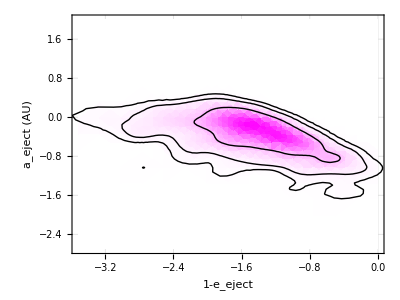

```mathematica
thermalcont=Show[{sdh3,cp}]
```

## CDF of mergers: comparison with Kritos+‘s Fig 5

```mathematica
timemerge//Length
```

1503

```mathematica
mergetimes = Log10[timemerge/(10^6 π 10^7)];
```

```mathematica
𝒟=EmpiricalDistribution[mergetimes]
```

DataDistribution[…]

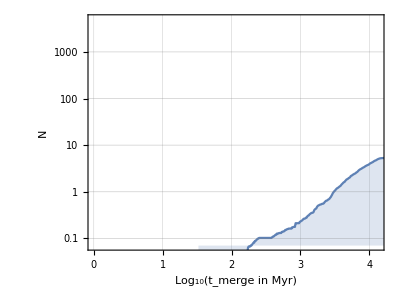

```mathematica
mergercdf=DiscretePlot[5.3CDF[𝒟,x],{x,0,5,.01},ScalingFunctions->{None,"Log"},Frame->True,LabelStyle->{(FontFamily->"Times"), Black},FrameLabel-> {Style["Log_10(t_merge in Myr)"],Style["N"]},BaseStyle->{FontSize->20},GridLines->Automatic,ColorFunction->(Blend[{Magenta,Magenta},#]&),PlotRange->{{0,4.13},{0.07,5000}},AspectRatio->0.74]
```